```mathematica
SetDirectory@NotebookDirectory[]
```

D:\works\Examples\WinBUGSinMathematica

```mathematica
WinBUGSPATH="d:/programs/WinBUGS/WinBUGS14/WinBUGS14.exe";
ScriptPATH=StringReplace[NotebookDirectory[],"\\"->"/"]<>"runscript.txt";
WinBUGSCommand=WinBUGSPATH<>" /PAR "<>ScriptPATH;
```

```mathematica
(* using Run[] for calling WinBUGS *)
Run[WinBUGSCommand]
```

0

```mathematica
(* using R via R2WinBUGS for calling WinBUGS *)
<<RLink`;
InstallR[];
```

```mathematica
REvaluate["{
library(\"R2WinBUGS\")
modelfile <- \"D:/works/Examples/WinBUGSinMathematica/model.txt\";
data<-list(x = c(8.0, 15.0, 22.0, 29.0, 36.0), xbar = 22, N = 30, T = 5,	
		Y = structure(.Data =   c(151, 199, 246, 283, 320,
							 145, 199, 249, 293, 354,
							 147, 214, 263, 312, 328,
							 155, 200, 237, 272, 297,
							 135, 188, 230, 280, 323,
							 159, 210, 252, 298, 331,
							 141, 189, 231, 275, 305,
							 159, 201, 248, 297, 338,
							 177, 236, 285, 350, 376,
							 134, 182, 220, 260, 296,
							 160, 208, 261, 313, 352,
							 143, 188, 220, 273, 314,
							 154, 200, 244, 289, 325,
							 171, 221, 270, 326, 358,
							 163, 216, 242, 281, 312,
							 160, 207, 248, 288, 324,
							 142, 187, 234, 280, 316,
							 156, 203, 243, 283, 317,
							 157, 212, 259, 307, 336,
							 152, 203, 246, 286, 321,
							 154, 205, 253, 298, 334,
							 139, 190, 225, 267, 302,
							 146, 191, 229, 272, 302,
							 157, 211, 250, 285, 323,
							 132, 185, 237, 286, 331,
							 160, 207, 257, 303, 345,
							 169, 216, 261, 295, 333,
							 157, 205, 248, 289, 316,
							 137, 180, 219, 258, 291,
							 153, 200, 244, 286, 324),
						.Dim = c(30,5)));

par2keep<-list(\"alpha0\",\"beta.c\",\"sigma\");

init<-list(list(alpha = c(250, 250, 250, 250, 250, 250, 250, 250, 250, 250, 250, 250, 250, 250, 250, 
					250, 250, 250, 250, 250, 250, 250, 250, 250, 250, 250, 250, 250, 250, 250),
		beta  = c(6, 6, 6, 6, 6, 6, 6, 6, 6, 6, 6, 6, 6, 6, 6, 
					6, 6, 6, 6, 6, 6, 6, 6, 6, 6, 6, 6, 6, 6, 6),			
		 alpha.c = 150, beta.c = 10, 
		 tau.c = 1, sigma.alpha = 1, sigma.beta = 1))


output<-bugs(
   model.file=file.path(modelfile),
   data=data,inits=init,
   parameters.to.save = par2keep,
   n.chains=1,
   n.iter=10000,
summary.only=TRUE,
  bugs.directory=(\"d:/programs/WinBUGS/WinBUGS14\"),
 working.directory=(\"D:/works/Examples/WinBUGSinMathematica/\"));

}"];
```

```mathematica
UninstallR[]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

D:\works\Examples\WinBUGSinMathematica

```mathematica
(* load coda and its index *)
codaIndex=Partition[ReadList["codaIndex.txt",Word],3];
codaCH1=Partition[ReadList["coda1.txt",Word],2];
```

```mathematica
codaObj[node_]:=ToExpression@codaCH1[[#1;;#2,2]]&@@(ToExpression@(codaIndex[[Position[codaIndex,node]//Flatten//First]]//Rest))
```

```mathematica
codaObj["sigma"]
```

{13.68,13.12,12.22,14.62,14.44,13.92,14.91,13.1,13.81,13.04,14.68,12.54,14.87,11.6,13.28,14.24,14.47,13.92,12.98,13.34,14.55,12.53,13.67,12.73,16.37,15.39,13.81,14.11,14.34,13.05,14.46,13.39,13.24,14.21,13.22,11.76,12.59,13.44,13.28,12.86,14.52,13.15,14.64,13.78,14.18,13.96,13.46,15.79,12.36,13.34,14.03,13.99,16.42,13.78,16.12,13.24,13.14,13.96,12.38,13.87,14.23,14.32,14.83,13.24,13.67,13.31,13.31,13.49,13.,14.11,13.48,12.66,13.99,15.02,14.59,13.42,14.04,13.34,14.96,11.26,16.1,14.01,13.86,13.62,12.14,14.39,15.21,14.13,12.99,15.82,13.42,13.33,13.8,13.61,14.46,15.35,13.02,16.,13.92,13.17,12.65,14.39,15.1,14.43,14.04,15.19,15.05,13.8,12.93,14.36,12.73,13.05,13.76,13.12,12.4,12.98,13.16,16.4,11.47,12.4,14.69,13.13,13.13,13.97,13.,13.25,13.92,14.8,13.92,13.64,13.14,12.62,12.88,13.62,12.84,13.02,14.12,13.36,12.31,12.15,12.78,13.21,14.2,14.46,15.79,13.24,12.95,14.71,13.17,13.69,14.5,14.72,13.03,14.32,12.66,12.12,13.46,12.65,14.08,13.1,15.84,14.75,16.03,12.85,13.95,12.95,14.45,14.14,12.09,12.28,12.46,13.6,13.62,15.07,15.21,14.42,14.53,13.42,14.49,14.61,13.34,11.92,12.74,14.11,14.13,13.27,15.85,12.82,14.76,14.44,12.4,13.92,13.06,12.83,13.65,13.33,13.49,13.87,13.35,14.56,13.74,11.57,13.12,13.76,13.48,13.31,13.67,14.71,12.73,12.69,14.14,12.99,12.15,12.76,12.58,13.44,12.85,13.89,14.66,13.35,13.23,14.48,14.17,14.77,14.16,13.01,13.53,13.4,12.99,12.24,14.13,13.91,14.33,14.58,13.47,14.43,14.14,13.38,12.95,13.51,13.64,12.91,13.94,13.58,13.52,13.84,15.43,14.2,12.16,12.59,13.67,14.01,14.74,12.56,13.71,14.04,13.08,14.15,13.84,15.14,14.73,14.03,13.54,14.72,14.56,14.97,13.5,12.35,14.2,13.32,12.59,12.31,14.73,13.78,14.62,13.65,13.77,12.64,12.66,12.13,13.2,12.67,13.81,13.09,13.68,13.65,13.44,13.75,13.35,14.38,13.75,13.3,14.28,16.3,14.1,13.13,15.16,13.66,14.1,13.7,14.25,14.16,13.37,14.96,12.91,13.38,14.57,12.88,14.14,12.77,14.5,12.85,13.17,13.62,13.62,12.71,13.55,13.76,14.,12.84,12.7,14.99,12.75,12.58,12.82,13.81,14.9,14.58,12.93,14.47,14.17,14.13,12.98,13.12,13.46,13.52,14.73,13.1,14.4,12.89,13.47,13.74,13.78,12.89,15.43,13.21,11.99,15.11,15.82,13.49,12.3,15.39,12.78,13.84,13.01,14.03,14.26,14.27,14.37,14.01,13.54,14.27,13.97,13.92,14.36,12.74,14.43,12.72,14.77,13.02,12.88,13.38,13.69,14.8,13.27,13.16,13.19,13.01,13.45,13.03,11.68,13.94,14.76,14.6,13.33,14.16,12.93,12.71,13.33,13.18,14.24,13.98,13.05,12.94,13.45,13.22,12.68,14.7,14.21,12.86,13.69,12.93,13.39,14.1,14.2,15.33,14.4,14.26,12.97,13.01,13.25,13.57,14.23,15.44,12.38,14.67,14.82,14.54,13.5,12.75,14.17,12.78,13.76,13.84,14.5,13.67,13.61,13.3,12.78,14.19,14.35,13.76,13.,13.99,13.59,12.8,14.3,13.75,13.33,13.36,14.11,13.09,12.83,14.48,13.28,14.06,12.79,13.65,13.4,12.92,14.8,13.93,13.29,13.04,13.11,12.85,14.11,12.44,14.29,14.67,13.81,14.42,14.04,15.45,14.93,13.98,11.58,15.06,14.39,14.5,13.41,12.52,13.08,14.12,13.84,12.54,13.22,13.23,13.33,14.37,13.33,12.87,16.28,12.39,14.85,12.01,13.71,13.34,12.69,12.13,11.49,14.42,11.02,13.1,12.13,14.03,12.85,12.44,13.23,12.87,13.09,14.37,14.3,14.95,14.79,12.9,13.75,14.11,15.37,14.09,14.01,12.14,13.46,11.88,13.06,13.42,14.84,12.58,15.28,13.61,15.42,14.3,14.12,14.23,13.58,13.98,11.68,14.21,13.26,12.61,13.67,13.04,12.99,13.52,15.57,11.99,14.14,13.51,13.74,14.51,12.87,14.05,13.25,15.97,14.69,13.18,13.43,13.25,12.88,12.58,12.51,13.24,13.75,14.43,14.12,14.22,15.9,13.93,13.97,14.73,14.24,13.49,13.06,15.42,12.97,13.31,15.06,12.76,16.13,14.64,13.31,14.05,13.68,12.94,12.66,13.5,12.42,13.37,14.07,14.37,15.32,13.01,13.22,13.08,14.94,13.57,14.07,13.1,14.02,13.6,13.91,12.64,11.93,13.21,13.25,12.65,13.9,13.58,13.11,13.51,14.58,12.29,14.21,13.09,14.31,13.07,14.23,13.2,13.9,15.01,13.85,11.68,15.14,13.78,13.32,13.79,15.61,15.65,13.9,13.64,13.38,12.93,13.29,14.31,13.15,13.28,14.47,12.72,14.62,14.65,15.09,14.4,13.07,13.28,13.97,14.13,13.89,13.89,15.05,11.96,14.4,12.93,14.86,15.03,14.34,12.62,13.46,13.19,13.43,12.71,14.2,14.87,15.01,15.27,13.04,13.75,14.15,14.51,14.04,12.85,13.3,13.01,12.49,13.26,15.77,14.36,13.61,14.7,13.87,13.17,12.44,14.63,12.74,12.19,11.87,15.04,14.49,15.01,12.03,13.17,15.01,13.09,12.82,14.05,13.45,13.56,13.56,14.24,15.07,13.43,12.63,13.29,13.94,14.25,15.57,15.85,14.35,14.45,14.9,12.89,13.67,14.45,13.78,14.31,14.08,14.65,13.82,14.83,14.77,15.68,13.28,14.25,15.17,12.88,14.09,14.21,13.76,14.42,14.88,13.72,12.88,12.32,12.32,13.05,13.23,13.81,13.08,12.76,12.65,12.88,12.54,12.52,13.47,13.3,12.54,13.98,13.87,13.69,14.22,13.78,14.65,14.01,12.96,13.88,12.81,13.13,12.87,14.43,13.08,14.24,12.72,14.21,13.93,15.02,14.78,12.59,12.15,13.58,14.,14.1,15.81,11.71,14.86,15.17,13.19,13.11,14.17,14.73,14.67,12.84,13.23,13.55,12.28,13.57,12.32,11.9,13.73,12.49,14.44,14.16,14.6,13.68,13.36,12.79,12.46,13.74,12.06,15.,13.85,13.4,13.83,13.77,14.39,13.48,15.22,12.41,14.,13.74,14.37,13.03,13.92,12.33,14.06,13.01,13.87,13.19,13.79,12.89,13.75,13.71,13.52,13.27,12.87,12.98,13.97,15.76,14.18,13.88,15.16,13.68,13.65,13.72,14.64,12.92,13.63,13.86,13.25,12.35,12.46,13.85,14.46,14.94,14.08,14.82,13.71,13.68,15.14,12.57,13.09,14.45,14.7,14.05,13.81,14.27,12.33,17.1,13.15,13.27,12.1,12.37,16.19,12.59,12.74,12.62,13.3,12.53,13.79,14.79,12.26,15.39,12.85,13.44,12.9,14.14,14.43,12.69,14.25,13.86,14.02,12.36,13.71,15.53,12.61,11.46,13.1,14.05,14.,13.79,15.39,13.4,14.17,13.62,13.59,14.07,12.2,15.02,14.32,13.88,12.97,12.87,13.48,13.26,12.91,14.62,13.78,13.39,15.75,13.73,15.06,14.85,12.96,15.93,15.22,14.15,12.66,14.01,12.34,13.44,12.99,12.67,13.61,13.48,13.86,13.56,12.71,13.91,13.63,13.18,13.67,12.31,13.76,11.98,13.,15.77,14.45,14.26,12.9,12.49,14.81,13.35,13.16,13.53,12.89,14.08,14.94,12.52,14.55,13.99,12.37,12.26,15.05,13.26,13.45,13.73,13.64,14.17,13.59,13.99,13.44,13.36,13.52,15.39,13.33,14.48,12.77,13.49,14.55,14.34,13.45,12.39,14.92,12.74,13.15,13.66,13.69,13.09,14.99,14.32,12.41,13.22,13.5,14.68,13.89,12.7,13.12,13.81,14.57,13.38,13.39,13.31,12.36,12.29,14.1,12.56,14.06,12.82,12.84,13.94,13.04,13.96,13.75,13.39,13.19,13.28,12.44,13.82,14.46,12.33,13.54,15.41}

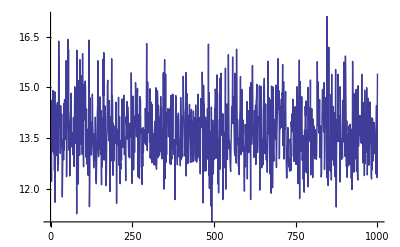

```mathematica
ListPlot[codaObj["sigma"],Joined->True]
```

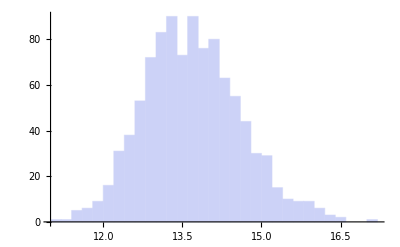

```mathematica
Histogram[codaObj["sigma"]]
```